# Olsenlab Magnetic Field simulations

## Initialization

```mathematica
<< Radia`; (*Load Radia*)
radFldUnits[]  (*Show the units in use *)
nseg = 50; (* Number of segmentations. Lower == faster simulations, cruder geometry *)
radFldCmpCrt[10^4]; (* Set the absolute precision for field computations *)
```

Radia Version: 4.32 is loaded

Radia is copyright ESRF, France.

Portions copyright Synchrotron SOLEIL, France.

Portions copyright Wolfram Research, Inc.

Physical units currently in use:
Length:  mm
Angle:  radian
Electric current:  A
Electric current density:  A/mm^2
Magnetization:  Tesla
Magnetic field induction:  Tesla
Magnetic field strength:  Tesla
Magnetic field integral along a line:  Tesla mm
Magnetic field vector-potential:  Tesla mm
Force:  Newton

```mathematica
hbar = 1.054571800*10^-34;(* (Js) *)
h = hbar*2π;(* (Js) *)
u = 1.66051*10^-27;(* atomic mass unit (kg) *)
kB = 1.380648 10^-23;(* Boltzmann constant (J/K) *)
c=2.9979 10^8; (* Speed of light m/s *)
muB=9.274 10^-24;
μ0=4π 10^-7;
hbareV=4.13566766 10^-15;
heV = hbareV*2π;
kBeV=8.61733034 10^-5;
Na=6.022 10^23;
eVJ=1.60218 10^-19;
mLi = 6 u;
ΓLi = 2 π 5.87 10^6;
λLi=671 10^-9;
ρCu=1.7 10^-8;(*resistivity of copper in Ohm m*)
ρBrass=9 10^-8;(*resistivity of copper in Ohm m*)
```

```mathematica
currents={-195,195,10,-10,0,0,261};(*currents for MOT, MOTH, Bias, BiasH, Curv, CurvH, ZS in A*)
```

```mathematica
currents={0,0,416,416,-123,-123,0};(*currents for MOT, MOTH, Bias, BiasH, Curv, CurvH, ZS in A*)
```

```mathematica
currents={195,195,0,0,0,0,0};(*currents for MOT, MOTH, Bias, BiasH, Curv, CurvH, ZS in A*)
```

## MOT Coils

The MOT coils will be wound from 1/4” circular copper tubing with insulation. This is stock from McMaster-Carr (https://www.mcmaster.com/3041K11)

```mathematica
tMOT =8; (*Thickness of the wire+coatings*)
rintubeMOT=2.413; (*Inner radius of tubing*)
routtubeMOT=3.175;(*Outer radius of tubing*)
turnMOT = 4; (*Number of turns of wire on coil*)
layerMOT = 4; (*Number of layers of wire on coil*)
rinMOT =80; (*Inner radius of coil*)
routMOT =rinMOT + turnMOT*tMOT; (*Outer radius of coil*)
IMOT = currents⟦1⟧; (*Current flowing through coil*)
IMOTH = currents⟦2⟧; (*Current flowing through coil*)
sepMOT =67 (*77; (*Separation between inner surfaces of coils*)*)
AMOT=π*10^-6(routtubeMOT^2-rintubeMOT^2);(*cross-section area of copper in m^2*)
lenMOT = 2π(rinMOT*turnMOT+Sum[n,{n,1,turnMOT-1}]*tMOT)*layerMOT*.001;(*length of MOT copper in m*)
RMOT=ρCu*lenMOT/AMOT;(*resistance of one MOT coil*)
VMOT=IMOT*2*RMOT;(*voltage drop for both MOT coils*)
PMOT=IMOT^2*2*RMOT;(*power dissipated in both MOT coils*)
LMOT=μ0 (turnMOT*layerMOT)^2(rinMOT+1.5*tMOT)*.001*(Log[8(rinMOT+1.5*tMOT)/routtubeMOT]-1.75);(*Self-inductance of one side of MOT coils*)
τMOT=LMOT/RMOT;
flowMOT=((140^1.85(2rintubeMOT/25.4)^4.87(72))/(4.52 (lenMOT*3.28)))^(.54)*.00006309;(*flow rate in gpm-> m^3/s*)
ReMOT=flowMOT*2*rintubeMOT 10^-3/(8.9 10^-7*π*rintubeMOT^2 10^-6);(*Reynolds number for cooling water*)
dT=PMOT/(998*flowMOT*4150);(*change in water temperature flowing through MOT coils*)
Grid[{{"MOT","R_coil / Ω","L_coil / H","τ / s","I / A", "V_tot / V","P_tot / W"},{"",RMOT,LMOT,τMOT,IMOT,VMOT,PMOT},{"Re","dV/dt / gpm","dV/dt / m^3/s", "ΔT / K","l / m"},{ReMOT,flowMOT/.00006309,flowMOT,dT,lenMOT}},Frame->All]

(*Defining the MOT Coils *)
MOTcoil = radObjArcCur[{0,0,(-(sepMOT+turnMOT*tMOT))/2}, {rinMOT, routMOT}, {0, 2π}, layerMOT*tMOT, nseg,IMOT/tMOT^2]; 
MOTcoilH = radObjArcCur[{0,0,(sepMOT+turnMOT*tMOT)/2}, {rinMOT,routMOT}, {0, 2π}, layerMOT*tMOT, nseg, IMOTH/tMOT^2];

(*Concantenate the two coils into one object*)
Clear[MOTgrp];
MOTgrp = radObjCnt[{MOTcoil, MOTcoilH}];

(*Plotting the Geometry of the MOT coils*)
(*RadPlot3DOptions[];
drM = radObjDrw[MOTgrp];
radObjDrwAtr[drM,Red];
Show[Graphics3D[drM, PlotLabel->"MOT Coils", BaseStyle->{14, FontFamily -> "Times"}]]*)
```

67

MOT | R_coil / Ω | L_coil / H | τ / s | I / A | V_tot / V | P_tot / W
 | 0.0117537 | 0.000109386 | 0.00930647 | -195 | -4.58395 | 893.87
Re | dV/dt / gpm | dV/dt / m^3/s | ΔT / K | l / m |  | 
23338.2 | 1.24788 | 0.0000787289 | 2.74133 | 9.24885 |  |

LinkObject::linkd: Unable to communicate with closed link LinkObject["C:\Program Files\Wolfram Research\Mathematica\13.1\AddOns\Applications\Radia\Radia.exe",41555,10].

LinkObject::linkn: Argument LinkObject["C:\Program Files\Wolfram Research\Mathematica\13.1\AddOns\Applications\Radia\Radia.exe",41555,10] in LinkWrite[LinkObject["C:\Program Files\Wolfram Research\Mathematica\13.1\AddOns\Applications\Radia\Radia.exe",41555,10],CallPacket[17,{0.,0.,49.5,80.,112.,0.,6.28319,32.,50,3.04688,«2»}]] has an invalid LinkObject number; the link may be closed.

LinkObject::linkn: Argument LinkObject["C:\Program Files\Wolfram Research\Mathematica\13.1\AddOns\Applications\Radia\Radia.exe",41555,10] in LinkWrite[LinkObject["C:\Program Files\Wolfram Research\Mathematica\13.1\AddOns\Applications\Radia\Radia.exe",41555,10],CallPacket[21,{{$Failed,$Failed}}]] has an invalid LinkObject number; the link may be closed.

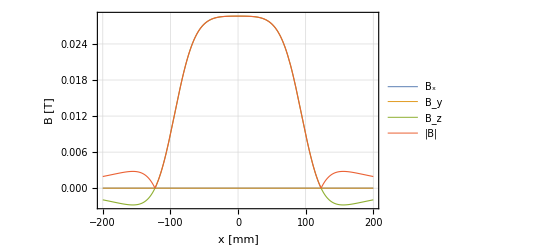

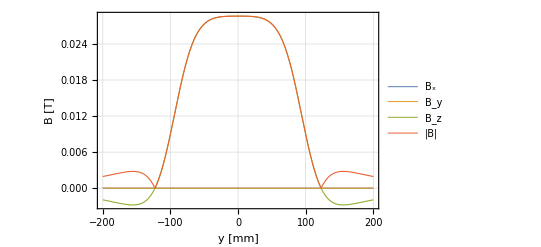

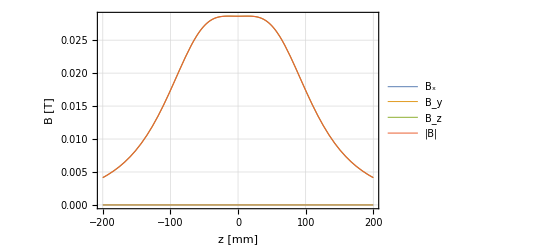

MOT | B / T | ∂B/∂z / T/mm | ∂^2 B/∂z^2 / T/mm^2
 | {3.73384×10^-14,1.80853×10^-9,0.0286322} | {1.74668×10^-15,1.35627×10^-8,-5.18301×10^-13} | {6.7312×10^-16,1.50721×10^-8,2.90617×10^-7}
∂B/∂x / T/mm | ∂^2 B/∂x^2 / T/mm^2 | ∂B/∂z / G/cm | ∂^2 B/∂z^2 / G/cm^2
{2.59301×10^-13,-1.50711×10^-9,6.55725×10^-15} | {-1.30146×10^-17,2.26066×10^-7,-1.45309×10^-7} | {1.74668×10^-10,0.00135627,-5.18301×10^-8} | {6.7312×10^-10,0.0150721,0.290617}
∂B/∂x / G/cm | ∂^2 B/∂x^2 / G/cm^2 | ∂B/∂z / uT/m | ∂^2 B/∂z^2 / uT/m^2
{2.59301×10^-8,-0.000150711,6.55725×10^-10} | {-1.30146×10^-11,0.226066,-0.145309} | {1.74668×10^-6,13.5627,-0.000518301} | {0.00067312,15072.1,290617.}

```mathematica
(* Plotting the MOT Magnetic Field and Calculating Other Parameters*)

RadPlotOptions[];

Plot[{radFld[MOTgrp, "bx", {x,0,0}],radFld[MOTgrp, "by", {x,0,0}],radFld[MOTgrp, "bz", {x,0,0}],Sqrt[radFld[MOTgrp, "bx", {x,0,0}]^2+radFld[MOTgrp, "by", {x,0,0}]^2+radFld[MOTgrp, "bz", {x,0,0}]^2]}, {x, -200, 200}, FrameLabel -> {"x [mm]", "B [T]", "MOT B-Field"},PlotLegends->{"B_x","B_y","B_z","|B|"}]
Plot[{radFld[MOTgrp, "bx", {0,y,0}],radFld[MOTgrp, "by", {0,y,0}],radFld[MOTgrp, "bz", {0,y,0}],Sqrt[radFld[MOTgrp, "bx", {0,y,0}]^2+radFld[MOTgrp, "by", {0,y,0}]^2+radFld[MOTgrp, "bz", {0,y,0}]^2]}, {y, -200, 200}, FrameLabel -> {"y [mm]", "B [T]", "MOT B-Field"},PlotLegends->{"B_x","B_y","B_z","|B|"}]
simMOTPlot=Plot[{radFld[MOTgrp, "bx", {0,0,z}],radFld[MOTgrp, "by", {0,0,z}],radFld[MOTgrp, "bz", {0,0,z}],Sqrt[radFld[MOTgrp, "bx", {0,0,z}]^2+radFld[MOTgrp, "by", {0,0,z}]^2+radFld[MOTgrp, "bz", {0,0,z}]^2]}, {z, -200, 200}, FrameLabel -> {"z [mm]", "B [T]", "MOT B-Field"},PlotLegends->{"B_x","B_y","B_z","|B|"}]
dStep=.1;
BMOT = radFld[MOTgrp, "b", {0,0,0}];
gradMOTx=(1/12*radFld[MOTgrp, "b", {-2 dStep,0,0}]-2/3*radFld[MOTgrp, "b", {-dStep,0,0}]+2/3*radFld[MOTgrp, "b", { dStep,0,0}]-1/12 radFld[MOTgrp, "b", {2 dStep,0,0}])/dStep;
curvMOTx=(-1/12*radFld[MOTgrp, "b", {-2 dStep,0,0}]+4/3*radFld[MOTgrp, "b", {- dStep,0,0}]-5/2*radFld[MOTgrp, "b", {0,0,0}]+4/3*radFld[MOTgrp, "b", {dStep,0,0}]-1/12 radFld[MOTgrp, "b", {2 dStep,0,0}])/dStep^2;
gradMOTz=(1/12*radFld[MOTgrp, "b", {0,0,-2 dStep}]-2/3*radFld[MOTgrp, "b", {0,0,-dStep}]+2/3*radFld[MOTgrp, "b", {0,0,dStep}]-1/12 radFld[MOTgrp, "b", {0,0,2 dStep}])/dStep;
curvMOTz=(-1/12*radFld[MOTgrp, "b", {0,0,-2 dStep}]+4/3*radFld[MOTgrp, "b", {0,0,-dStep}]-5/2*radFld[MOTgrp, "b", {0,0,0}]+4/3*radFld[MOTgrp, "b", {0,0,dStep}]-1/12 radFld[MOTgrp, "b", {0,0,2 dStep}])/dStep^2;
Grid[{{"MOT","B / T","∂B/∂z / T/mm" ,"∂^2 B/∂z^2 / T/mm^2"},{"",BMOT,gradMOTz,curvMOTz},{"∂B/∂x / T/mm" ,"∂^2 B/∂x^2 / T/mm^2","∂B/∂z / G/cm" ,"∂^2 B/∂z^2 / G/cm^2"},{gradMOTx,curvMOTx,gradMOTz*10^4*10,curvMOTz*10^4*10^2},{"∂B/∂x / G/cm" ,"∂^2 B/∂x^2 / G/cm^2","∂B/∂z / uT/m" ,"∂^2 B/∂z^2 / uT/m^2"},{gradMOTx*10^4*10,curvMOTx*10^4*10^2,gradMOTz*10^6*10^3,curvMOTz*10^6*10^6}},Frame->All]
```

```mathematica
rawDat=Import["Z:\\Data\\2023\\2023-02\\2023-02-10\\MOT coil 1.xlsx"];
```

```mathematica
posMOT=rawDat[[1,2;;-1,1]]
fieldMOT=rawDat[[1,2;;-1,5]]
```

{560.,550.,540.,530.,520.,510.,500.,490.,480.,470.,460.,450.,440.,430.,420.,410.,400.,390.,380.,370.,360.,350.,340.,330.,320.,300.,290.}

{0.0127,0.0156,0.0179,0.0213,0.0254,0.0296,0.0346,0.0404,0.0475,0.0551,0.0638,0.074,0.0826,0.0921,0.0994,0.1046,0.1066,0.1047,0.1005,0.0931,0.0846,0.0745,0.0651,0.0558,0.0479,0.0337,0.0293}

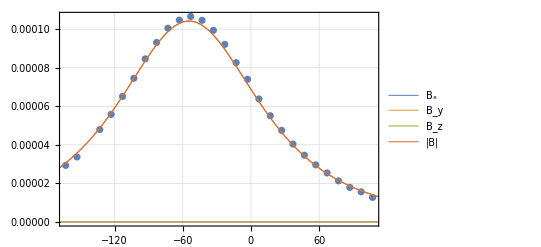

```mathematica
datMOTPlot=ListPlot[{Transpose[{posMOT-453,fieldMOT 10^-3}]}];
Show[datMOTPlot,simMOTPlot]
```

## Bias and curvature coils

Copper arcs for bias and curvature fields

```mathematica
nlayersBC = 26;
iangBC = 0.5*2.79*π/180; (*ring split angle*)
sepBC = 31.012; (*Position of the base ('brass' part)*)
tBrassBC = 6.35; (*Thickness of the base*)
tCuBC = 1.02; (*Thickness of the copper layers*)
tSpacerBC = 0.25; (*Thickness of the spacers*)
angHoffBC=0*π;
HdirBC=1;

Clear[zposBC]; 
(*Function for the center of each element according to its layer*)
zposBC[layer_]:= sepBC/2 + tBrassBC + (layer-1)*(tCuBC+tSpacerBC);

IB =currents⟦3⟧;(* Current in bias (outer) coil *)
IBH =currents⟦4⟧;(* Current in bias (outer) coil *)
IC = currents⟦5⟧; (*Current in first coil*)
ICH = currents⟦6⟧; (*Current in first coil*)

rinC = 18; (*Inner radius of the cois*)
routC = 31; (*Outer radius of the coils *)
rinB = 33; (*Inner radius of the cois*)
routB = 47;(*Outer radius of the coils *)

RBrassC=ρBrass*(2π)/(tBrassBC Log[routC/rinC]);(*resistance of brass curvature coil*)
RCuC=ρCu*(2π)/(10^-3 tCuBC Log[routC/rinC]);(*resistance of one curvature coil*)
RspacerC=ρCu*(tSpacerBC 10^-3)/(π(routC^2-rinC^2)/10 10^-6);(*resistance of one curvature spacer*)
RBrassB=ρBrass*(2π)/(10^-3 tBrassBC Log[routB/rinB]);(*resistance of brass bias coil*)
RCuB=ρCu*(2π)/(10^-3 tCuBC Log[routB/rinB]);(*resistance of one bias coil*)
RspacerB=ρCu*(tSpacerBC 10^-3)/(π(routB^2-rinB^2)/10 10^-6);(*resistance of one curvature spacer*)
Rscrew=ρBrass*((zposBC[nlayersBC]-zposBC[1]+4)10^-3)/(π 2.5^2 10^-6);
RC=Rscrew+RBrassC+nlayersBC*(RCuC+RspacerC);(*resistance of entire curvature assembly on one side*)
RB=Rscrew+RBrassB+nlayersBC*(RCuB+RspacerB);(*resistance of entire bias assembly on one side*)
VC=IC*2*RC;(*voltage drop for both curvature coils*)
VB=IB*2*RB;(*voltage drop for both bias coils*)
PC=IC^2*2*RC;(*power dissipated in both curavture coils*)
PB=IB^2*2*RB;(*power dissipated in both curavture coils*)
LC=μ0/(4π) (1+nlayersBC)^2 rinC*.001*30;(*Self-inductance of one side of curvature coils*)
LB=μ0/(4π) (1+nlayersBC)^2 rinB*.001*30;(*Self-inductance of one side of bias coils*)
τC=LC/RC;
τB=LB/RB;
lenBC = 2*(zposBC[nlayersBC]-zposBC[1])*.001; (*length of water tube in m*)
ReBC=6 10^-7*((2 10 tSpacerBC)/(10+tSpacerBC)) 10^-3/(8.9 10^-7*(10 tSpacerBC) 10^-6);(*Reynolds number for cooling water*)
flowBC=3.8 10^-3/60;(*5*((140^1.85(nlayersBC(2 10 tSpacerBC)/(10+tSpacerBC)/25.4)^4.87(72))/(4.52 (lenBC*3.28)))^(.54)*.00006309;*)(*flow rate in gpm-> m^3/s*)
dTC=PC/(998*flowBC*4186);(*change in water temperature flowing through curvature coils*)
dTB=PB/(998*flowBC*4186);(*change in water temperature flowing through bias coils*)
Grid[{{"Curvature","R_coil / Ω","L_coil / H","τ / s","I / A", "V_tot / V","P_tot / W"},{"",RC,LC,τC,IC,VC,PC},{"Re","dV/dt / gpm","dV/dt / m^3/s","dV/dt / l/m", "ΔT / K","l / m"},{ReBC,flowBC/.00006309,flowBC,flowBC*60*1000,dTC,lenBC}},Frame->All]
Grid[{{"Bias","R_coil / Ω","L_coil / H","τ / s","I / A", "V_tot / V","P_tot / W"},{"",RB,LB,τB,IB,VB,PB},{"Re","dV/dt / gpm","dV/dt / m^3/s","dV/dt / l/m", "ΔT / K","l / m"},{ReBC,flowBC/.00006309,flowBC,flowBC*60*1000,dTB,lenBC}},Frame->All]


(*Let's define the brass bases first *)
brassC = radObjArcCur[{0,0,sepBC/2+tBrassBC/2}, {rinC, routC}, {iangBC, 2π-iangBC}, tBrassBC, nseg, IC/(tBrassBC*(routC-rinC))];
brassB = radObjArcCur[{0,0,sepBC/2+tBrassBC/2}, {rinB, routB}, {π+iangBC, 3π-iangBC}, tBrassBC, nseg, IB/(tBrassBC*(routB-rinB))];
brassCH = radObjArcCur[{0,0,-sepBC/2-tBrassBC/2}, {rinC, routC}, {angHoffBC+iangBC,angHoffBC+2π-iangBC}, tBrassBC, nseg, ICH/(tBrassBC*(routC-rinC))];
brassBH = radObjArcCur[{0,0,-sepBC/2-tBrassBC/2}, {rinB, routB}, {angHoffBC+π+iangBC, angHoffBC+3π-iangBC}, tBrassBC, nseg, IBH/(tBrassBC*(routB-rinB))];
screwC =  radObjRecCur[{1/2(routC+rinC)*Cos[(0-1) π/5+π/10],1/2(routC+rinC)*Sin[(0-1) π/5+π/10],(zposBC[1]+zposBC[nlayersBC]+35)/2}, {5,5,zposBC[nlayersBC]-zposBC[1]+35}, {0,0,IC/(5)^2}];
screwB =  radObjRecCur[{1/2(routB+rinB)*Cos[(5-1) π/5+π/10],1/2(routB+rinB)*Sin[(5-1) π/5+π/10],(zposBC[1]+zposBC[nlayersBC]+35)/2}, {5,5,zposBC[nlayersBC]-zposBC[1]+35}, {0,0,IB/(5)^2}];
screwCH =  radObjRecCur[{1/2(routC+rinC)*Cos[angHoffBC-(0-1) π/5-π/10],1/2(routC+rinC)*Sin[angHoffBC-(0-1) π/5-π/10],-(zposBC[1]+zposBC[nlayersBC]+35)/2}, {5,5,zposBC[nlayersBC]-zposBC[1]+35}, {0,0,-IC/(5)^2}];
screwBH =  radObjRecCur[{1/2(routB+rinB)*Cos[angHoffBC-(5-1) π/5-π/10],1/2(routB+rinB)*Sin[angHoffBC-(5-1) π/5-π/10],-(zposBC[1]+zposBC[nlayersBC]+35)/2}, {5,5,zposBC[nlayersBC]-zposBC[1]+35}, {0,0,-IB/(5)^2}];
rodC =  radObjRecCur[{(routC-5/2)*Cos[(nlayersBC-0) π/5],(routC-5/2)*Sin[(nlayersBC-0) π/5],(2zposBC[nlayersBC]+35)/2}, {5,5,35}, {0,0,IC/(5)^2}];
rodB =  radObjRecCur[{(routB-5/2)*Cos[π+(nlayersBC-0) π/5],(routB-5/2)*Sin[π+(nlayersBC-0) π/5],(2zposBC[nlayersBC]+35)/2}, {5,5,35}, {0,0,IB/(5)^2}];
rodCH =  radObjRecCur[{(routC-5/2)*Cos[angHoffBC-(nlayersBC-0) π/5],(routC-5/2)*Sin[angHoffBC-(nlayersBC-0) π/5],-(2zposBC[nlayersBC]+35)/2}, {5,5,35}, {0,0,-IC/(5)^2}];
rodBH =  radObjRecCur[{(routB-5/2)*Cos[angHoffBC-π-(nlayersBC-0) π/5],(routB-5/2)*Sin[angHoffBC-π-(nlayersBC-0) π/5],-(2zposBC[nlayersBC]+35)/2}, {5,5,35}, {0,0,-IB/(5)^2}];
(*Initialize a container and put them in it*)
Clear[BCgrp];
BCgrp = radObjCnt[{brassC,brassB, brassCH, brassBH}];
radObjAddToCnt[BCgrp,{ screwC,screwB, rodC,rodB, screwCH, screwBH, rodCH, rodBH}];
(*Now, encode all the separate parts of the two coils and append them to the container we just created *)

For[layer = 1, layer ≤  nlayersBC, 
(*First, let's do one coil *)
spacerC =  radObjRecCur[{1/2(routC+rinC)*Cos[(layer-1) π/5+π/10],1/2(routC+rinC)*Sin[(layer-1) π/5+π/10],zposBC[layer]+tSpacerBC/2}, {routC-rinC,routC-rinC,tSpacerBC}, {0,0,-0*IC/(routC-rinC)^2}];
copperC = radObjArcCur[{0,0,zposBC[layer]+tSpacerBC+tCuBC/2}, {rinC, routC}, {(layer) π/5+iangBC, (layer) π/5+2 π-iangBC},tCuBC, nseg,IC/(tCuBC*(routC-rinC))];
spacerB =  radObjRecCur[{1/2(routB+rinB)*Cos[π+(layer-1) π/5+π/10],1/2(routB+rinB)*Sin[π+(layer-1) π/5+π/10],zposBC[layer]+tSpacerBC/2}, {routB-rinB,routB-rinB,tSpacerBC}, {0,0,-0*IB/(routB-rinB)^2}];
copperB = radObjArcCur[{0,0,zposBC[layer]+tSpacerBC+tCuBC/2}, {rinB, routB}, {π+(layer) π/5+iangBC, π+(layer) π/5+2 π-iangBC},tCuBC, nseg,IB/(tCuBC*(routB-rinB))];
(*Now, for the second coil*)
spacerCH =  radObjRecCur[{1/2(routC+rinC)*Cos[angHoffBC-(layer-1) π/5-π/10],1/2(routC+rinC)*Sin[angHoffBC-(layer-1) π/5-π/10],-zposBC[layer]-tSpacerBC/2}, {routC-rinC,routC-rinC,tSpacerBC}, {0,0,-0*ICH/(routC-rinC)^2}];
copperCH = radObjArcCur[{0,0,-zposBC[layer]-tSpacerBC-tCuBC/2}, {rinC, routC}, {angHoffBC-(layer) π/5-2 π+iangBC,angHoffBC-(layer) π/5-iangBC},tCuBC, nseg,ICH/(tCuBC*(routC-rinC))];
spacerBH =  radObjRecCur[{1/2(routB+rinB)*Cos[angHoffBC-π-(layer-1) π/5-π/10],1/2(routB+rinB)*Sin[angHoffBC-π-(layer-1) π/5-π/10],-zposBC[layer]-tSpacerBC/2}, {routB-rinB,routB-rinB,tSpacerBC}, {0,0,0IBH/(routB-rinB)^2}];
copperBH = radObjArcCur[{0,0,-zposBC[layer]-tSpacerBC-tCuBC/2}, {rinB, routB}, {angHoffBC-π-(layer) π/5-2 π+iangBC,angHoffBC-π-(layer) π/5-iangBC},tCuBC, nseg,IBH/(tCuBC*(routB-rinB))];
(*Put everything into the container *)
radObjAddToCnt[BCgrp,{ spacerC,spacerB,spacerCH,spacerBH}];
radObjAddToCnt[BCgrp,{ copperC,copperB,copperCH,copperBH}];
layer++; 
(*layer+=nlayersBC-1;*)];
(*matSS=radMatLin[{1.005,1.005},10^-15]; (* define SS material *)
chamberSS1=radObjRecMag[{19.5,31.5,12.5},{63,39,2.1},{0,0,1}];
chamberSS2=radObjRecMag[{31.5,-19.5,12.5},{39,63,2.1},{0,0,1}];
chamberSS3=radObjRecMag[{-19.5,-31.5,12.5},{63,39,2.1},{0,0,1}];
chamberSS4=radObjRecMag[{-31.5,19.5,12.5},{39,63,2.1},{0,0,1}];
chamberSS1H=radObjRecMag[{19.5,31.5,-12.5},{63,39,2.1},{0,0,1}];
chamberSS2H=radObjRecMag[{31.5,-19.5,-12.5},{39,63,2.1},{0,0,1}];
chamberSS3H=radObjRecMag[{-19.5,-31.5,-12.5},{63,39,2.1},{0,0,1}];
chamberSS4H=radObjRecMag[{-31.5,19.5,-12.5},{39,63,2.1},{0,0,1}];
Clear[BCSSgrp];
BCSSgrp = radObjCnt[{chamberSS1,chamberSS2,chamberSS3,chamberSS4,chamberSS1H,chamberSS2H,chamberSS3H,chamberSS4H}];
radMatApl[BCSSgrp,matSS];
radObjDivMag[BCSSgrp,{{10,1},{10,1},{3,1}},{"pln",{1,0,0},{0,1,0},{0,0,1}}]
intM=radRlxPre[BCSSgrp,BCgrp];
radRlxMan[intM,3,1500,0];
BCgrp=radObjCnt[{BCgrp,BCSSgrp}];*)
RadPlot3DOptions[];
drBC = radObjDrw[BCgrp];
Show[Graphics3D[drBC, PlotLabel->"Bias & Curvature", BaseStyle->{14, FontFamily-> "Times"}]]
```

Curvature | R_coil / Ω | L_coil / H | τ / s | I / A | V_tot / V | P_tot / W
 | 0.00517311 | 0.000039366 | 0.00760973 | -123 | -1.27259 | 156.528
Re | dV/dt / gpm | dV/dt / m^3/s | dV/dt / l/m | ΔT / K | l / m | 
131.543 | 1.00386 | 0.0000633333 | 3.8 | 0.591602 | 0.0635 |

Bias | R_coil / Ω | L_coil / H | τ / s | I / A | V_tot / V | P_tot / W
 | 0.00811511 | 0.000072171 | 0.00889341 | 416 | 6.75177 | 2808.74
Re | dV/dt / gpm | dV/dt / m^3/s | dV/dt / l/m | ΔT / K | l / m | 
131.543 | 1.00386 | 0.0000633333 | 3.8 | 10.6157 | 0.0635 |

```mathematica
totFld[pos_]:=Norm[radFld[BCgrp, "b", pos+{0,0,0}]]
dStep=.01;
BBC = radFld[BCgrp, "b", {0,0,0}];
gradBCx=(1/12*radFld[BCgrp, "b", {-2 dStep,0,0}]-2/3*radFld[BCgrp, "b", {-dStep,0,0}]+2/3*radFld[BCgrp, "b", { dStep,0,0}]-1/12 radFld[BCgrp, "b", {2 dStep,0,0}])/dStep;
curvBCx=(-1/12*radFld[BCgrp, "b", {-2 dStep,0,0}]+4/3*radFld[BCgrp, "b", {- dStep,0,0}]-5/2*radFld[BCgrp, "b", {0,0,0}]+4/3*radFld[BCgrp, "b", {dStep,0,0}]-1/12 radFld[BCgrp, "b", {2 dStep,0,0}])/dStep^2;
gradBCz=(1/12*radFld[BCgrp, "b", {0,0,-2 dStep}]-2/3*radFld[BCgrp, "b", {0,0,-dStep}]+2/3*radFld[BCgrp, "b", {0,0,dStep}]-1/12 radFld[BCgrp, "b", {0,0,2 dStep}])/dStep;
curvBCz=(-1/12*radFld[BCgrp, "b", {0,0,-2 dStep}]+4/3*radFld[BCgrp, "b", {0,0,-dStep}]-5/2*radFld[BCgrp, "b", {0,0,0}]+4/3*radFld[BCgrp, "b", {0,0,dStep}]-1/12 radFld[BCgrp, "b", {0,0,2 dStep}])/dStep^2;
gradBCm={(1/12*totFld[{-2 dStep,0,0}]-2/3*totFld[{-dStep,0,0}]+2/3*totFld[{dStep,0,0}]-1/12 totFld[{2 dStep,0,0}])/dStep,(1/12*totFld[{0,-2 dStep,0}]-2/3*totFld[{0,-dStep,0}]+2/3*totFld[{0, dStep,0}]-1/12 totFld[{0,2 dStep,0}])/dStep,
(1/12*totFld[{0,0,-2 dStep}]-2/3*totFld[{0,0,-dStep}]+2/3*totFld[{0,0,dStep}]-1/12 totFld[{0,0,2 dStep}])/dStep};
curvBCm={(-1/12*totFld[{-2 dStep,0,0}]+4/3*totFld[{- dStep,0,0}]-5/2*totFld[{0,0,0}]+4/3*totFld[{dStep,0,0}]-1/12 totFld[{2 dStep,0,0}])/dStep^2,(-1/12*totFld[{0,-2 dStep,0}]+4/3*totFld[{0,- dStep,0}]-5/2*totFld[{0,0,0}]+4/3*totFld[{0,dStep,0}]-1/12 totFld[{0,2 dStep,0}])/dStep^2,(-1/12*totFld[{0,0,-2 dStep}]+4/3*totFld[{0,0,- dStep}]-5/2*totFld[{0,0,0}]+4/3*totFld[{0,0, dStep}]-1/12 totFld[{0,0,2 dStep}])/dStep^2};
factor=1;(*factor to expand Bx and By *)
Grid[{{"Bias/Curv","B / T","∂B/∂z / T/mm" ,"∂^2 B/∂z^2 / T/mm^2"},{totFld[{0,0,0}],BBC,gradBCz,curvBCz},{"∂B/∂x / T/mm" ,"∂^2 B/∂x^2 / T/mm^2","∂B/∂z / G/cm" ,"∂^2 B/∂z^2 / G/cm^2"},{gradBCx,curvBCx,gradBCz*10^4*10,curvBCz*10^4*10^2},{"∂B/∂x / G/cm" ,"∂^2 B/∂x^2 / G/cm^2","∂B/∂z / uT/m" ,"∂^2 B/∂z^2 / uT/m^2"},{gradBCx*10^4*10,curvBCx*10^4*10^2,gradBCz*10^6*10^3,curvBCz*10^6*10^6},{"B/ T (G)" ,"∂B/∂q / uT/m (G/cm)" ,"∂^2 B/∂q^2 / uT/m^2 (G/cm^2)",""},{totFld[{0,0,0}],gradBCm*10^6*10^3,curvBCm*10^6*10^6,""},{totFld[{0,0,0}]*10^4,gradBCm*10^4*10^1,curvBCm*10^4*10^2,""}},Frame->All]
Plot[{radFld[BCgrp, "bx", {x,0,0}] factor,radFld[BCgrp, "by", {x,0,0}] factor,radFld[BCgrp, "bz", {x,0,0}],totFld[{x,0,0}]}, {x, -100, 100}, Frame->True,FrameLabel -> {"x [mm]", "B [T]", "Bias/Curvature B-Field"},PlotLegends->{"B_x","B_y","B_z","|B|"},PlotRange->All]
Plot[{radFld[BCgrp, "bx", {0,y,0}] factor,radFld[BCgrp, "by", {0,y,0}] factor,radFld[BCgrp, "bz", {0,y,0}],totFld[{0,y,0}]}, {y, -100, 100}, Frame->True,FrameLabel -> {"y [mm]", "B [T]", "Bias/Curvature B-Field"},PlotLegends->{"B_x","B_y","B_z","|B|"},PlotRange->All]
Plot[{radFld[BCgrp, "bx", {0,0,z}]factor,radFld[BCgrp, "by", {0,0,z}]factor,radFld[BCgrp, "bz", {0,0,z}],totFld[{0,0,z}]}, {z, -100, 100}, Frame->True,FrameLabel -> {"z [mm]", "B [T]", "Bias/Curvature B-Field"},PlotLegends->{"B_x","B_y","B_z","|B|"},PlotRange->All]
(*In Smale et al 2019, the curvature was around 500 uT/m^2*)
```

Bias/Curv | B / T | ∂B/∂z / T/mm | ∂^2 B/∂z^2 / T/mm^2
0.109932 | {0.000540757,-0.000121849,0.109931} | {1.91762×10^-6,0.0000377433,5.70458×10^-10} | {9.24609×10^-7,-5.6755×10^-6,0.000030876}
∂B/∂x / T/mm | ∂^2 B/∂x^2 / T/mm^2 | ∂B/∂z / G/cm | ∂^2 B/∂z^2 / G/cm^2
{-4.56658×10^-6,4.3254×10^-8,3.10845×10^-6} | {5.5628×10^-7,0.0000662287,-0.0000161204} | {0.191762,3.77433,0.0000570458} | {0.924609,-5.6755,30.876}
∂B/∂x / G/cm | ∂^2 B/∂x^2 / G/cm^2 | ∂B/∂z / uT/m | ∂^2 B/∂z^2 / uT/m^2
{-0.456658,0.0043254,0.310845} | {0.55628,66.2287,-16.1204} | {1917.62,37743.3,0.570458} | {924609.,-5.6755×10^6,3.0876×10^7}
B/ T (G) | ∂B/∂q / uT/m (G/cm) | ∂^2 B/∂q^2 / uT/m^2 (G/cm^2) | 
0.109932 | {3083.35,-3.10842,-33.0282} | {-1.55457×10^7,-1.46243×10^7,3.0949×10^7} | 
1099.32 | {0.308335,-0.000310842,-0.00330282} | {-15.5457,-14.6243,30.949} |

## Zeeman Slower

```mathematica
Clear[ZSgrp];
ZSgrp = radObjCnt[{}];
IZS = currents⟦7⟧; (*Current in the ZS coils*)
rinZS = 13.7;
routZS = 35;
(*discsZS0 = 25.4 Flatten[Table[#[[1]],#[[2]]]&/@{{0.125,1},{.025,9},{.032,40},{.04,20},{.05,20},{.063,40},{.08,0},{.093,0},{.125,20}}];
(*discsZS0=25.4 Table[Nearest[{.025,.032,.04,.05,.063,.08,.093,.125},1.3(100.1-n)^(-.7)][[1]],{n,100}];*)
discsZS=discsZS0;
changes=Rest[Position[Abs[Differences[discsZS0]],_?Positive]]; (*get indices where changes happen for dithering*)
({discsZS[[#]],discsZS[[#+1]]}={discsZS[[#+1]],discsZS[[#]]})&/@changes;
({discsZS[[#-2]],discsZS[[#+3]]}={discsZS[[#+3]],discsZS[[#-2]]})&/@changes;
({discsZS[[#-5]],discsZS[[#+6]]}={discsZS[[#+6]],discsZS[[#-5]]})&/@changes;
StringForm["Number of discs: ``",Length[discsZS]] (*Output number of discs *)
gapsZS0 = 25.4 Flatten[Table[#[[1]],#[[2]]]&/@{{.025,100},{.05,30},{.063,17},{.125,3}}];
(*discsZS0=25.4 Table[Nearest[{.025,.032,.04,.05,.063,.08,.093,.125},1.3(100.1-n)^(-.7)][[1]],{n,100}];*)
gapsZS=gapsZS0;
changesG=Position[Abs[Differences[gapsZS0]],_?Positive]
({gapsZS[[#]],gapsZS[[#+1]]}={gapsZS[[#+1]],gapsZS[[#]]})&/@changesG;
({gapsZS[[#-2]],gapsZS[[#+3]]}={gapsZS[[#+3]],gapsZS[[#-2]]})&/@changesG;
({gapsZS[[#-5]],gapsZS[[#+6]]}={gapsZS[[#+6]],gapsZS[[#-5]]})&/@changesG;*)
discsZS = 25.4*{
.125,.04,.04,.04,.04,.04,.04,.04,.08,.04,.0400,
.04,.08,.04,.04,.04,.08,.04,.04,.04,.08000,
.04,.08,.04,.08,.04,.08,.04,.08,.04,.08000,
.08,.04,.08,.08,.04,.08,.08,.08,.04,.08000,
.08,.08,.04,.08,.08,.08,.08,.04,.08, .08000,
.08,.08,.08,.04,.08,.08,.08,.08,.08,.08000,
.08,.04,.08,.08,.08,.08,.08,.04,.08,.08000,
.08,.08,.08,.08,.08,.08,.125,.08,.08,.08000,
.08,.08,.125,.08,.08,.08,.08,.125,.08,.08000,
.08,.125,.08,.125,.08,.125,.08,.08,.08,.08000,
.125,.125,.125,.125,.125}
StringForm["Number of discs: ``",Length[discsZS]] (*Output number of discs *)
gapsZS = 25.4*{
.025,.025,.025,.025,.025,.025,.025,.025,.025,.025,.025,
.025,.025,.025,.025,.025,.025,.025,.025,.025,.025,
.025,.05,.025,.025,.025,.025,.025,.025,.025, .05000,
.025,.025,.025,.025,.025,.025,.025,.025,.025,.025000,
.025,.025,.05,.025,.025,.025,.025,.025,.025,.05000,
.025,.025,.025,.05,.025,.025,.025,.05,.025,.05000,
.025,.05,.025,.05,.05,.025,.05,.05,.05,.025000,
.05,.05,.05,.025,.05,.025,.05,.05,.05,.025000,
.05,.05,.05,.05,.05,.075,.05,.05,.075,.05000,
.075,.075,.05,.075,.075,.1,.1,.125,.125,.15000,
.175,.175,.175,.125,0}
StringForm["Number of gaps: ``",Length[gapsZS]](*Output number of gaps *)
zposZS[layer_]:=If[layer ==1,0,Accumulate[discsZS+gapsZS]⟦layer-1⟧]
maxlayerZS=Length[gapsZS];
lenZS = zposZS[maxlayerZS]+discsZS[[maxlayerZS]];
(*Now, encode all the separate parts of the two coils and append them to the container we just created *)
For[layer = 1, layer < maxlayerZS,
(*copper =  radObjArcCur[{0,0,zposZS[layer]+0.5 discsZS[[layer]]}, {rinZS, routZS}, {If[EvenQ[layer],0,π],If[EvenQ[layer],22π/18,40 π/18]},discsZS⟦layer⟧, nseg,IZS/(discsZS⟦layer⟧*(routZS-rinZS))];*)copper =  radObjArcCur[{0,0,zposZS[layer]+0.5 discsZS[[layer]]}, {rinZS, routZS}, {If[EvenQ[layer],0,π],If[EvenQ[layer],π,2π]},discsZS⟦layer⟧, nseg,IZS/(discsZS⟦layer⟧*(routZS-rinZS))];
copperplug =  radObjRecCur[{If[EvenQ[layer],-1,1] 0.5(routZS+rinZS)Sin[11π/18] ,If[EvenQ[layer],1,-1] 0.5(routZS+rinZS)Cos[11π/18],zposZS[layer]+discsZS⟦layer⟧ +0.5 gapsZS⟦layer⟧}, {routZS-rinZS,routZS-rinZS,gapsZS⟦layer⟧},{0,0,IZS/(routZS-rinZS)^2}];
(*Put everything into the container *)
radObjAddToCnt[ZSgrp,{copper,copperplug}];layer++];
copper =  radObjArcCur[{0,0,zposZS[maxlayerZS]+0.5 discsZS[[maxlayerZS]]}, {rinZS, routZS}, {If[If[EvenQ[maxlayerZS],π,0]+π/3,EvenQ[maxlayerZS],2π,π]-π/3},discsZS⟦maxlayerZS⟧, nseg,IZS/(discsZS⟦maxlayerZS⟧*(routZS-rinZS))];
radObjAddToCnt[ZSgrp,{copper}];

RCuZS=Total[ρCu*(2π)/(10^-3 discsZS Log[routZS/rinZS])](*resistance of all ZS coils*)
RspacerZS=Total[ρCu*(gapsZS 10^-3)/((routZS-rinZS)^2 10^-6)](*resistance of all ZS spacers*)

RZS=RCuZS+RspacerZS;(*resistance of entire ZS coil*)
VZS=IZS*RZS;(*voltage drop for both curvature coils*)
PZS=IZS^2*RZS;(*power dissipated in both curavture coils*)
LZS=μ0/(4π) (maxlayerZS)^2 rinZS*.001*10;(*Self-inductance of ZS coils*)
τZS=LZS/RZS;
(*lenZS = 2*(zposBC[nlayersBC]-zposBC[1])*.001; (*length of water tube in m*)*)
(*ReZS=6 10^-7*((2 10 tSpacerBC)/(10+tSpacerBC)) 10^-3/(8.9 10^-7*(10 tSpacerBC) 10^-6);*)(*Reynolds number for cooling water*)
flowZS=3.8 10^-3/60;(*5*((140^1.85(nlayersBC(2 10 tSpacerBC)/(10+tSpacerBC)/25.4)^4.87(72))/(4.52 (lenBC*3.28)))^(.54)*.00006309;*)(*flow rate in gpm-> m^3/s*)
dTZS=PZS/(998*flowZS*4186);(*change in water temperature flowing through curvature coils*)
Grid[{{"Bias","R_coil / Ω","L_coil / H","τ / s","I / A", "V_tot / V","P_tot / W"},{"",RZS,LZS,τZS,IZS,VZS,PZS},{"Re","dV/dt / gpm","dV/dt / m^3/s","dV/dt / l/m", "ΔT / K","l / mm"},{0,flowZS/.00006309,flowZS,flowZS*60*1000,dTZS,lenZS}},Frame->All]
```

{3.175,1.016,1.016,1.016,1.016,1.016,1.016,1.016,2.032,1.016,1.016,1.016,2.032,1.016,1.016,1.016,2.032,1.016,1.016,1.016,2.032,1.016,2.032,1.016,2.032,1.016,2.032,1.016,2.032,1.016,2.032,2.032,1.016,2.032,2.032,1.016,2.032,2.032,2.032,1.016,2.032,2.032,2.032,1.016,2.032,2.032,2.032,2.032,1.016,2.032,2.032,2.032,2.032,2.032,1.016,2.032,2.032,2.032,2.032,2.032,2.032,2.032,1.016,2.032,2.032,2.032,2.032,2.032,1.016,2.032,2.032,2.032,2.032,2.032,2.032,2.032,2.032,3.175,2.032,2.032,2.032,2.032,2.032,3.175,2.032,2.032,2.032,2.032,3.175,2.032,2.032,2.032,3.175,2.032,3.175,2.032,3.175,2.032,2.032,2.032,2.032,3.175,3.175,3.175,3.175,3.175}

Number of discs: 106

{0.635,0.635,0.635,0.635,0.635,0.635,0.635,0.635,0.635,0.635,0.635,0.635,0.635,0.635,0.635,0.635,0.635,0.635,0.635,0.635,0.635,0.635,1.27,0.635,0.635,0.635,0.635,0.635,0.635,0.635,1.27,0.635,0.635,0.635,0.635,0.635,0.635,0.635,0.635,0.635,0.635,0.635,0.635,1.27,0.635,0.635,0.635,0.635,0.635,0.635,1.27,0.635,0.635,0.635,1.27,0.635,0.635,0.635,1.27,0.635,1.27,0.635,1.27,0.635,1.27,1.27,0.635,1.27,1.27,1.27,0.635,1.27,1.27,1.27,0.635,1.27,0.635,1.27,1.27,1.27,0.635,1.27,1.27,1.27,1.27,1.27,1.905,1.27,1.27,1.905,1.27,1.905,1.905,1.27,1.905,1.905,2.54,2.54,3.175,3.175,3.81,4.445,4.445,4.445,3.175,0.}

Number of gaps: 106

0.00732375

4.44944×10^-6

Bias | R_coil / Ω | L_coil / H | τ / s | I / A | V_tot / V | P_tot / W
 | 0.0073282 | 0.000153933 | 0.0210056 | 261 | 1.91266 | 499.204
Re | dV/dt / gpm | dV/dt / m^3/s | dV/dt / l/m | ΔT / K | l / mm | 
0 | 1.00386 | 0.0000633333 | 3.8 | 1.88676 | 318.389 |

```mathematica
RadPlot3DOptions[];
drZS = radObjDrw[ZSgrp];
Show[Graphics3D[drZS, PlotLabel->"Bitter Zeeman Slower", BaseStyle->{14, FontFamily-> "Times"}]]
```

## Combine all coils

```mathematica
RadPlotOptions[];
lenZSMOT=111.35; (* distance from last ZS coil to chamber center*)
(*Rotating and translating the MOT to be at the rear of the Zeeman Slower *) 
rotator = radTrfRot[{0,0,0},{1,0,0},π/2];zs=Table[ z,{z,0,500}];
```

```mathematica
Clear[Allgrp];
Allgrp = radObjCnt[{}];
Clear[ZSgrp2];
ZSgrp2 = radObjDpl[ZSgrp];
radObjAddToCnt[Allgrp,{ZSgrp2}];
translator = radTrfTrsl[{0,0,lenZS+lenZSMOT}];
Clear[MOTgrp2];
MOTgrp2 = radObjDpl[MOTgrp];
radTrfOrnt[MOTgrp2, rotator];
radTrfOrnt[MOTgrp2,translator];
radObjAddToCnt[Allgrp,{MOTgrp2}];
Clear[BCgrp2];
BCgrp2 = radObjDpl[BCgrp];
radTrfOrnt[BCgrp2, rotator];
radTrfOrnt[BCgrp2,translator];
radObjAddToCnt[Allgrp,{BCgrp2}];
(*RadPlot3DOptions[];
drZS = radObjDrw[Allgrp];
Show[Graphics3D[drZS, PlotLabel->"Bitter Zeeman Slower", BaseStyle->{14, FontFamily-> "Times"}]]*)
(*Calculating the B-field and other parameters*)

fields=Table[radFld[Allgrp, "Bz", {0,0,z}],{z,0,500}];
maxField=Max[fields];
zMax=zs[[Position[fields,maxField][[1,1]]]];
zMOT=FirstPosition[Evaluate[Table[radFld[Allgrp, "Bz", {0,0,z}],{z,0,500}]],_?(#<0&)]⟦1⟧
(*gradAllz=(1/12*radFld[Allgrp, "b", {0,0,zMOT-2 dStep}]-2/3*radFld[Allgrp, "b", {0,0,zMOT-dStep}]+2/3*radFld[Allgrp, "b", {0,0,zMOT+dStep}]-1/12 radFld[Allgrp, "b", {0,0,zMOT+2 dStep}])/dStep;
Grid[{{"All","∂B/∂z / T/mm" ,"∂B/∂z / G/cm" },{"",gradAllz,gradAllz*10^4*10}},Frame->All]*)
thick = ListPlot[Evaluate[Table[{zposZS[i],gapsZS⟦i⟧*.01},{i,1,maxlayerZS-1}]],PlotLegends->{"Spacers"},PlotMarkers->{Automatic,Scaled[0.01]}];
thick2 = ListPlot[Evaluate[Table[{zposZS[i],discsZS⟦i⟧*.01-.0005},{i,1,maxlayerZS}]],PlotStyle->Green,PlotLegends->{"Discs"},PlotMarkers->{Automatic,Scaled[0.01]}];(*D0=If[CF800,-250,-300]; (*laser detuning for ideal ZS field profile*)
vi=If[CF800,900,885];(*initial velocity for ideal ZS field profile*)
η=If[CF800,0.5,0.66];*)
ηs={2/3.5};
(*efficiency parameter for ideal ZS field profile*)
vis=√(.001 (zMOT-zMax)( 2 ηs (hbar 2 π ΓLi)/(2 mLi λLi))+30^2) 
D0s=((maxField muB)/hbar-(2π vis)/λLi)/(2π 10^6)
fieldMOT=Table[radFld[MOTgrp2, "Bz", {0,0,z}],{z,0,500}];(* getting parameters for optimum ZS curve, but offset for visualization*)
maxFieldMOT=Max[fieldMOT];
zMaxMOT=zs[[Position[fieldMOT,maxFieldMOT][[1,1]]]];
visMOT=√(.001 (zMOT-zMaxMOT)( 2 ηs (hbar 2 π ΓLi)/(2 mLi λLi))+30^2) ;
D0sMOT=((maxFieldMOT muB)/hbar-(2π visMOT)/λLi)/(2π 10^6);(*all these are meaningless*)
ZSfield=Plot[{hbar/muB(D0s 2 π 10^6+(2π)/λLi √(vis^2- 2 ηs (hbar 2 π ΓLi)/(2 mLi λLi) (z-zMax)/1000)),.0045+hbar/muB(D0sMOT 2 π 10^6+(2π)/λLi √(visMOT^2- 2 ηs (hbar 2 π ΓLi)/(2 mLi λLi) (z-zMaxMOT)/1000)),radFld[Allgrp, "Bz", {0,0,z}],radFld[ZSgrp, "Bz", {0,0,z}],radFld[MOTgrp2,"bz",{0,0,z}],radFld[BCgrp2,"bz",{0,0,z}],100 radFld[Allgrp, "Bx", {0,0,z}], If[Abs[z-zMOT] > 20, 0,-.002  .1(z-zMOT)]}, {z, 0, zMOT}, FrameLabel-> {"z [mm]", "B_z [T]", "Zeeman Slower field profile"},PlotLegends->{"B_opt / T","B_(z, tot) / T","B_(z, ZS) / T","B_(z, MOT) / T","B_(z, BC) / T","10 B_(x, tot) / T","MOT 20 G/cm"}] ;
resPlt=Plot[50(radFld[Allgrp, "Bz", {0,0,z}]-.004-hbar/muB(D0sMOT 2 π 10^6+(2π)/λLi √(visMOT^2- 2 ηs (hbar 2 π ΓLi)/(2 mLi λLi) (z-zMaxMOT)/1000))),{z, zMax, 350},ImageSize->{750,200},AspectRatio->2/7.5,PlotRange->{{0,zMOT},{-0.03,0.1}},FrameLabel-> {"z [mm]", "B_resid [T]"},PlotStyle->Gray];Show[ZSfield,resPlt,thick,thick2,ImageSize->{750,300},AspectRatio->3/7.5]

(*zeefield = Table[{z,radFld[Allgrp, "bz", {0,0,z}]}, {z, -100, 500}];
Export["BZSField_3.txt", zeefield, "Table"] ;*)
```

433

{913.442}

{-353.677}

```mathematica
Grid[{{"ZS copper",".04'' discs" ,".08'' discs",".125'' discs" },{"",Count[discsZS,x_/;x==25.4*.04],Count[discsZS,x_/;x==25.4*.08],Count[discsZS,x_/;x==25.4*.125]},{"spacers",".025''" ,".05''",".075''",".1''",".125''",".15''",".175''" },{"",Count[gapsZS,x_/;x==25.4*.025],Count[gapsZS,x_/;x==25.4*.05],Count[gapsZS,x_/;x==25.4*.075],Count[gapsZS,x_/;x==25.4*.1],Count[gapsZS,x_/;x==25.4*.125],Count[gapsZS,x_/;x==25.4*.15],Count[gapsZS,x_/;x==25.4*.175]}},Frame->All]
```

ZS copper | .04'' discs | .08'' discs | .125'' discs |  |  |  | 
 | 29 | 65 | 12 |  |  |  | 
spacers | .025'' | .05'' | .075'' | .1'' | .125'' | .15'' | .175''
 | 61 | 29 | 6 | 2 | 3 | 1 | 3

```mathematica
Count[discsZS,x_/;x==25.4*.125]
```

22

```mathematica
Transpose[{Range[71],discsZS/25.4,Rationalize[gapsZS/25.4]}]//TableForm
```

1 | 0.125 | 1/32
2 | 0.04 | 1/32
3 | 0.04 | 1/32
4 | 0.08 | 1/16
5 | 0.04 | 1/32
6 | 0.04 | 1/16
7 | 0.08 | 1/32
8 | 0.04 | 1/16
9 | 0.04 | 1/32
10 | 0.08 | 1/16
11 | 0.04 | 1/32
12 | 0.08 | 1/16
13 | 0.04 | 1/16
14 | 0.08 | 1/32
15 | 0.04 | 1/16
16 | 0.08 | 1/16
17 | 0.08 | 1/32
18 | 0.08 | 1/16
19 | 0.04 | 1/16
20 | 0.08 | 1/16
21 | 0.08 | 1/32
22 | 0.08 | 1/16
23 | 0.08 | 1/16
24 | 0.08 | 1/16
25 | 0.08 | 1/16
26 | 0.08 | 1/32
27 | 0.08 | 1/16
28 | 0.08 | 1/16
29 | 0.08 | 1/16
30 | 0.08 | 1/16
31 | 0.08 | 1/32
32 | 0.08 | 1/16
33 | 0.08 | 1/16
34 | 0.08 | 1/16
35 | 0.125 | 1/16
36 | 0.08 | 1/16
37 | 0.08 | 1/32
38 | 0.08 | 1/16
39 | 0.125 | 1/16
40 | 0.08 | 1/16
41 | 0.125 | 1/16
42 | 0.08 | 1/16
43 | 0.08 | 1/16
44 | 0.125 | 1/16
45 | 0.08 | 1/16
46 | 0.125 | 1/16
47 | 0.08 | 1/16
48 | 0.08 | 1/16
49 | 0.125 | 1/8
50 | 0.08 | 1/16
51 | 0.08 | 1/16
52 | 0.08 | 1/8
53 | 0.125 | 1/16
54 | 0.08 | 1/16
55 | 0.08 | 1/8
56 | 0.125 | 1/16
57 | 0.125 | 1/8
58 | 0.08 | 1/16
59 | 0.125 | 1/8
60 | 0.125 | 1/16
61 | 0.08 | 1/8
62 | 0.125 | 1/8
63 | 0.125 | 1/8
64 | 0.125 | 1/8
65 | 0.125 | 1/8
66 | 0.125 | 1/8
67 | 0.125 | 1/8
68 | 0.125 | 1/4
69 | 0.125 | 1/4
70 | 0.125 | 1/4
71 | 0.125 | 0

```mathematica
3160 0.3/10
```

94.8